# Associated Mathematica file for Proulx and Teotonio “Weak selection of phenotypic memory in periodic environments”

This notebook creates figures and results in the paper.  Phenotypes and environmental optima are on the interval -1 to 1, fitness is Exp[-eta^2 (z-z*)^2], and lambda is per-generation asymptotic log growth. Evaluate the notebook from top to bottom.

### Definitions

```mathematica
okabeIto=Apply[RGBColor,{{0,0,0},{0.9,0.6,0},{0.35,0.7,0.9},{0,0.6,0.5},{0.95,0.9,0.25},{0,0.45,0.7},{0.8,0.4,0},{0.8,0.6,0.7}},{1}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Analytic results for the derivative of the eigenvalues

#### Model and parameters

```mathematica
b={{beta1,1-beta1},{1-beta2,beta2}};
betaAssumptions=Element[{beta1,beta2},Reals]&&0<beta1<1&&0<beta2<1;
parameterRules=First[Solve[Join[Thread[{q1,q2}.b=={q1,q2}],{q1+q2==1,h==beta1+beta2-1}],{beta1,beta2,q1}]];
b=Simplify[b/.parameterRules];
assumptions=Element[{eta,h,q2,x},Reals]&&eta>0&&-1<h<1&&0<q2<1&&Element[k,Integers]&&k>=1&&(And@@(0<#<1&/@Flatten[b]));
w[e_,z_]:=DiagonalMatrix[{Exp[-eta^2],Exp[-eta^2*(e-z)^2]}];
```

#### Cycle and ancestral growth

```mathematica
cycle=MatrixPower[w[-1,x].b,k].MatrixPower[w[1,x].b,k];
polynomial=CharacteristicPolynomial[cycle,y];
characteristic=polynomial/.y->Exp[2*k*lambda[x]];
lambda0=FullSimplify[Log[Max@@Eigenvalues[w[-1,0].b]],assumptions]
```

-eta^2

#### Log-growth derivatives

```mathematica
rule0={lambda[0]->lambda0};
firstDerivative=FullSimplify[(D[characteristic,x]/.x->0)/.rule0,assumptions];
rule1=First[Solve[firstDerivative==0,Derivative[1][lambda][0]]];
secondDerivative=FullSimplify[(D[characteristic,{x,2}]/.x->0)/.Join[rule0,rule1],assumptions];
rule2=First[Solve[secondDerivative==0,Derivative[2][lambda][0]]];
lambda2=FullSimplify[Derivative[2][lambda][0]/.rule2,assumptions]
```

-2 eta^2 q2+(4 eta^4 (-k+h (4+h k)+h^k (-4 h+(-1+h^2) k)) (-1+q2) q2)/((-1+h)^2 (1+h^k) k)

#### Compact form

```mathematica
short=FullSimplify[lambda2/.{h^(2*k)->u^2,h^k->u},assumptions&&Element[u,Reals]&&-1<u<1];
compact=Collect[short,eta,Factor]/.u->h^k;
compact
```

-2 eta^2 q2+(4 eta^4 (4 h-4 h^(1+k)-k+h^2 k-h^k k+h^(2+k) k) (-1+q2) q2)/((-1+h)^2 (1+h^k) k)

Which is equivalent to the expression that we present

```mathematica
typesetForm = 2 eta^2 q2 (-1 + 2 eta^2 (1 - q2)
  ((1 + h)/(1 - h) - 4 h (1 - u)/(k (1 - h)^2 (1 + u))));
```

```mathematica
Simplify[typesetForm-compact/.{u->h^k}//Expand]
```

0

### Region plots for positive second derivatives

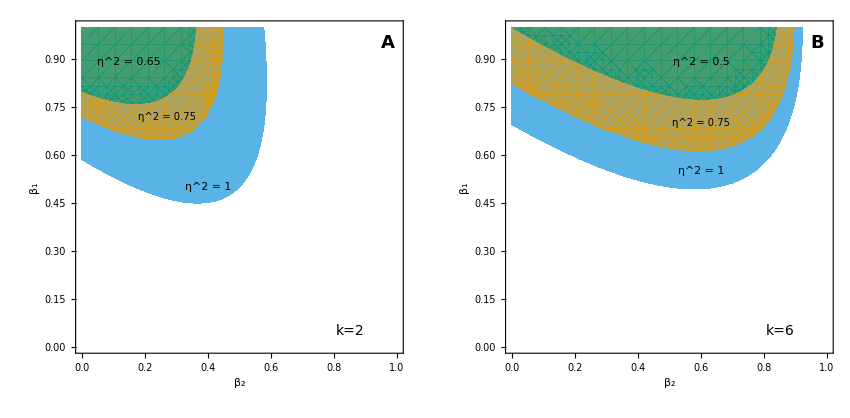

```mathematica
memoryRegionFigure=GraphicsRow[{D2k2=compact/.{h->β1+β2-1,q2->(1-β1)/(2-β1-β2)}/.{k->2};
colors={Directive[okabeIto⟦3⟧,Opacity[1]],Directive[okabeIto⟦2⟧,Opacity[0.6]],Directive[okabeIto⟦4⟧,Opacity[0.6]]};
Show[RegionPlot[(D2k2/.{eta->1})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[1]],BoundaryStyle->None,Epilog->Inset[Style["η^2 = 1",11,Black],{.4,.5}]],RegionPlot[(D2k2/.{eta->Sqrt[0.75]})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[2]],BoundaryStyle->None,Epilog->Inset[Style["η^2 = 0.75",11,Black],{.34,.76}]],RegionPlot[(D2k2/.{eta->Sqrt[0.65]})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[3]] ,BoundaryStyle->None] ,Frame->True,FrameLabel->{Style[Subscript[β, 2],24,Bold],Style[Subscript[β, 1],24,Bold]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.02],Epilog->{Inset[Style["η^2 = 0.75",10,Black],{.27,.72}],Inset[Style["η^2 = 1",11,Black],{.4,.5}],Inset[Style["η^2 = 0.65",11,Black],{.15,0.89}],Inset[Style["k=2",14,Black],{0.85,0.05}],Inset[Style["A",18,Black,Bold],{0.97,0.95}]}],



D2k6=compact/.{h->β1+β2-1,q2->(1-β1)/(2-β1-β2)}/.{k->6};


colors={Directive[okabeIto⟦3⟧,Opacity[1]],Directive[okabeIto⟦2⟧,Opacity[0.6]],Directive[okabeIto⟦4⟧,Opacity[0.6]]};
Show[RegionPlot[(D2k6/.{eta->1})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[1]],BoundaryStyle->None,Epilog->Inset[Style["η^2 = 1",11,Black],{.4,.5}]],RegionPlot[(D2k6/.{eta->Sqrt[0.75]})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[2]],BoundaryStyle->None,Epilog->Inset[Style["η^2 = 0.75",11,Black],{.34,.76}]],RegionPlot[(D2k6/.{eta->Sqrt[0.5]})>0,{β2,0,1},{β1,0,1},PlotStyle->colors[[3]] ,BoundaryStyle->None] ,Frame->True,FrameLabel->{Style[Subscript[β, 2],24,Bold],Style[Subscript[β, 1],24,Bold]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.02],Epilog->{Inset[Style["η^2 = 0.75",10,Black],{.6,.7}],Inset[Style["η^2 = 1",11,Black],{.6,.55}],Inset[Style["η^2 = 0.5",11,Black],{.6,0.89}],Inset[Style["k=6",14,Black],{0.85,0.05}],Inset[Style["B",18,Black,Bold],{0.97,0.95}]}] },Spacings->10,ImageSize->850]
```

```mathematica
Export["memory_invasion_regions.pdf",memoryRegionFigure];
```

### Main model definitions

```mathematica
SetDirectory[NotebookDirectory[]];

ClearAll[zOpt,w,fitness,transmissionMatrix,selectionMatrix,cycleMatrix,dominantEigenvalue2,lambdaExpression,gradientExpression,secondZ2Expression,lambdaCompiled,gradientCompiled,secondZ2Compiled,lambdaNumeric,etaFromSigma,sigmaFromEta,logit,invLogit,periodicPhenotypeCycle,mutualInformation,binaryEntropy,maximumInformation,relativeInformation,numericalFirstDerivativeCheck,firstZDerivativeNumeric,makeFirstDerivativeSurface,secondZDerivativeNumeric,makeSecondDerivativeSurface,firstDerivativeSurface,secondDerivativeSurface,simulateTrajectory,evolveToEquilibrium,makeTrajectoryFigure,makeMemoryRegionPanel];

okabeIto=Apply[RGBColor,{{0,0,0},{0.9,0.6,0},{0.35,0.7,0.9},{0,0.6,0.5},{0.95,0.9,0.25},{0,0.45,0.7},{0.8,0.4,0},{0.8,0.6,0.7}},{1}];

etaFromSigma[s_?NumericQ]:=1/(Sqrt[2] s);
sigmaFromEta[x_?NumericQ]:=1/(Sqrt[2] x);

zOpt[1]=-1;
zOpt[2]=1;

w[z_,e_Integer,eta_]:=Exp[-eta^2 (z-zOpt[e])^2];

transmissionMatrix[beta1_,beta2_]:={{beta1,1-beta1},{1-beta2,beta2}};

selectionMatrix[e_Integer,z1_,z2_,eta_]:=DiagonalMatrix[{w[z1,e,eta],w[z2,e,eta]}];

cycleMatrix[z1_,z2_,beta1_,beta2_,eta_,k_Integer]:=Module[{b=transmissionMatrix[beta1,beta2],a1,a2},a1=selectionMatrix[1,z1,z2,eta].b;
a2=selectionMatrix[2,z1,z2,eta].b;
MatrixPower[a1,k].MatrixPower[a2,k]];

dominantEigenvalue2[m_]:=(Tr[m]+Sqrt[Tr[m]^2-4 Det[m]])/2;

lambdaExpression[k_Integer]:=lambdaExpression[k]=Log[dominantEigenvalue2[cycleMatrix[z1,z2,beta1,beta2,eta,k]]]/(2 k);

gradientExpression[k_Integer]:=gradientExpression[k]=(D[lambdaExpression[k],#]&)/@{z1,z2,beta1,beta2};

secondZ2Expression[k_Integer]:=secondZ2Expression[k]=D[lambdaExpression[k],{z2,2}]/. {z1->0,z2->0};

lambdaCompiled[k_Integer]:=lambdaCompiled[k]=With[{expr=lambdaExpression[k]},Compile[{{z1,_Real},{z2,_Real},{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[expr]]];

gradientCompiled[k_Integer]:=gradientCompiled[k]=With[{expr=gradientExpression[k]},Compile[{{z1,_Real},{z2,_Real},{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[expr]]];

secondZ2Compiled[k_Integer]:=secondZ2Compiled[k]=With[{expr=secondZ2Expression[k]},Compile[{{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[Re[expr]]]];

lambdaNumeric[params_List,etaValue_?NumericQ,k_Integer]:=Module[{m=N[IdentityMatrix[2]],dominantRoot,b,a1,a2,scale,logScale=0.},b=transmissionMatrix[params[[3]],params[[4]]];
a1=N[selectionMatrix[1,params[[1]],params[[2]],etaValue].b];
a2=N[selectionMatrix[2,params[[1]],params[[2]],etaValue].b];
Do[m=m.a;
scale=Max[Abs[Flatten[m]]];
If[!TrueQ[scale>0.],Return[Indeterminate]];
m=m/scale;
logScale+=Log[scale],{a,Join[ConstantArray[a1,k],ConstantArray[a2,k]]}];
dominantRoot=Max[Abs[Eigenvalues[m]]];
If[!TrueQ[dominantRoot>0.],Return[Indeterminate]];
(logScale+Log[dominantRoot])/(2 k)];
```

### Compare to DME

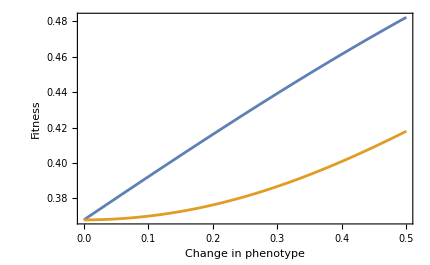

```mathematica
kValue=6;
etaValue=1;          
beta1Value=5/6; 
beta2Value=5/6;
epsilonMaximum=0.5;

lambdaAncestor=(Log[w[0,1,etaValue]]+Log[w[0,2,etaValue]])/2;

(*Deterministic maternal effect,with phenotypes {-eps/2,+eps/2}*)
dmeLogGrowth[eps_?NumericQ]:=(kValue-1)/(2 kValue) (Log[w[-eps/2,1,etaValue]]+Log[w[eps/2,2,etaValue]])+1/(2 kValue) (Log[w[eps/2,1,etaValue]]+Log[w[-eps/2,2,etaValue]]);

(*State-transmission mutant,with phenotypes {-eps/2,+eps/2}*)
stateLogGrowth[eps_?NumericQ]:=lambdaNumeric[{-eps/2,eps/2,beta1Value,beta2Value},etaValue,kValue];

dmeColor=RGBColor[0.80,0.20,0.15];
stateColor=RGBColor[0.00,0.45,0.70];



dmeComparisonFigure=Plot[{Exp[dmeLogGrowth[eps]],Exp[stateLogGrowth[eps]]},{eps,0,epsilonMaximum},Frame->True,FrameLabel->{"Change in phenotype","Fitness"},ImageSize->430,BaseStyle->{FontFamily->"Helvetica",12}]
```

```mathematica
Export["DMECompare.pdf",dmeComparisonFigure];
```

### Simulation

```mathematica
mainK=6;
mainEta=Sqrt[0.75];
mainInitialParameters={0.,0.1,0.99,0.01};
mainTolerance=1/10^4;
mainStepSize=1.;
mainMaxSteps=10000;

mainTrajectory=Module[{params=N[mainInitialParameters],gradFun=gradientCompiled[mainK],lamFun=lambdaCompiled[mainK],grad,effectiveGradient,index,records={},step=0,lam,info,maxGradient,x,env,pairedEnv,infoMaximum,m,eigensystem,dominantIndex,state,states,b,joint,pEnv,pPhen,mutualInfo},env=Join[ConstantArray[1,mainK],ConstantArray[2,mainK]];
pairedEnv=RotateLeft[env];
infoMaximum=If[mainK>2,N[1+(1/mainK) Log[2,1/mainK]+(1-1/mainK) Log[2,1-1/mainK]],Indeterminate];
While[step<=mainMaxSteps,grad=N[gradFun@@Join[params,{mainEta}]];
effectiveGradient=grad {2.,2.,1.,1.};
lam=N[lamFun@@Join[params,{mainEta}]];
(*Relative information,calculated directly*)info=If[mainK>2,m=N[cycleMatrix[params[[1]],params[[2]],params[[3]],params[[4]],mainEta,mainK]];
eigensystem=Eigensystem[Transpose[m]];
dominantIndex=First[Ordering[Re[eigensystem[[1]]],-1]];
state=Abs[Re[eigensystem[[2,dominantIndex]]]];
state=state/Total[state];
b=transmissionMatrix[params[[3]],params[[4]]];
(*Offspring frequencies paired with the next environment*)states=Table[state=state.selectionMatrix[e,params[[1]],params[[2]],mainEta].b;
state=state/Total[state];
state,{e,env}];
joint=Table[Total[Pick[states[[All,i]],pairedEnv,e]]/(2 mainK),{e,1,2},{i,1,2}];
pEnv=Total/@joint;
pPhen=Total[joint];
mutualInfo=Total[Flatten[Table[If[joint[[e,i]]>0,joint[[e,i]] Log[2,joint[[e,i]]/(pEnv[[e]] pPhen[[i]])],0.],{e,1,2},{i,1,2}]]];
N[mutualInfo/infoMaximum],Indeterminate];
maxGradient=Max[Abs[effectiveGradient]];
AppendTo[records,Join[{step},params,{lam,Norm[effectiveGradient],info}]];
If[maxGradient<=mainTolerance||step==mainMaxSteps,Break[]];
index=First[Ordering[Abs[effectiveGradient],-1]];
(*Shifted phenotype logit;ordinary retention logit*)x=If[index<=2,Log[(1+params[[index]])/(1-params[[index]])],Log[params[[index]]/(1-params[[index]])]];
x=x+mainStepSize effectiveGradient[[index]];
params[[index]]=If[index<=2,2/(1+Exp[-x])-1,1/(1+Exp[-x])];
step++;];
<|"Columns"->{"Step","z1","z2","beta1","beta2","lambda","EvolutionaryGradientNorm","RelativeInformation"},"Data"->records,"FinalParameters"->params,"Steps"->step|>];

trajectoryData=mainTrajectory["Data"];
```

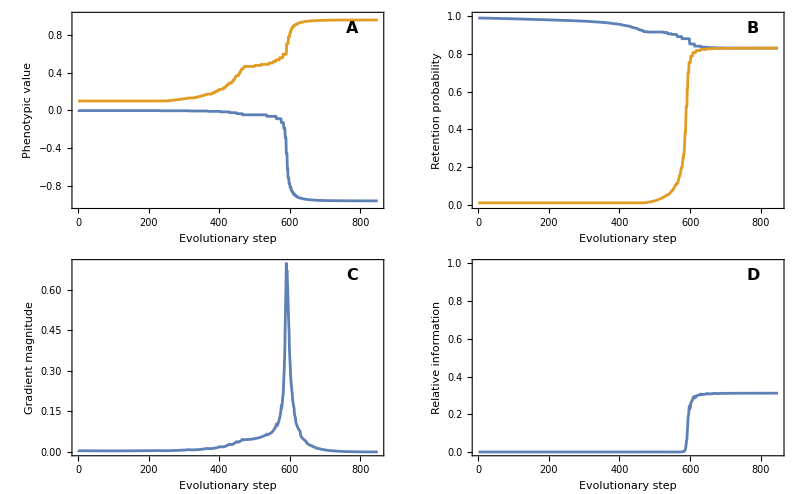

```mathematica
phenotypePlot=ListLinePlot[{trajectoryData[[All,{1,2}]],trajectoryData[[All,{1,3}]]},FrameTicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{Style["Evolutionary step",18,Bold],Style["Phenotypic value",18,Bold]},PlotRange->{All,{-1,1}},Epilog->{Inset[Style["A",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];

memoryPlot=ListLinePlot[{trajectoryData[[All,{1,4}]],trajectoryData[[All,{1,5}]]},FrameTicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{Style["Evolutionary step",18,Bold],Style["Retention probability",18,Bold]},PlotRange->{All,{0,1}},GridLines->{None,{1-1/mainK}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed],Epilog->{Inset[Style["B",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];

gradientPlot=ListLinePlot[trajectoryData[[All,{1,7}]],FrameTicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{Style["Evolutionary step",18,Bold],Style["Gradient magnitude",18,Bold]},PlotRange->All,Epilog->{Inset[Style["C",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];

informationPlot=ListLinePlot[trajectoryData[[All,{1,8}]],FrameTicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{Style["Evolutionary step",18,Bold],Style["Relative information",18,Bold]},PlotRange->{All,{0,1}},Epilog->{Inset[Style["D",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];

trajectoryFigure=GraphicsGrid[{{phenotypePlot,memoryPlot},{gradientPlot,informationPlot}},Spacings->{0.5,0.5},ImageSize->800];

trajectoryFigure
```

```mathematica
Export["evolutionary_trajectory.pdf",
trajectoryFigure];
```

### Origin vs maintenance

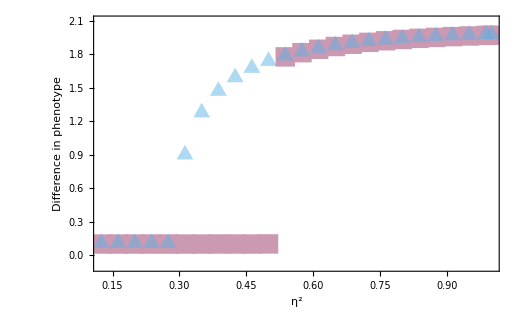

```mathematica
hysteresisK=6;
etaSquaredValues=N[Append[Range[1/8,79/80,3/80],1]];
noMemoryStartingParameters={0.,0.1,0.99,0.01};
hysteresisTolerance=1/10^4;
hysteresisStepSize=1.;
hysteresisMaximumSteps=30000;

(*Origin scan:increasing eta^2*)
originData=Module[{parameters=N[noMemoryStartingParameters],gradientFunction=gradientCompiled[hysteresisK],gradient,effectiveGradient,parameterToChange,step,x,etaValue},Table[If[Abs[parameters[[1]]]<0.1||Abs[parameters[[2]]]<0.1,parameters=N[noMemoryStartingParameters]];
etaValue=Sqrt[etaSquared];
step=0;
While[step<hysteresisMaximumSteps,gradient=N[gradientFunction[parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]],etaValue]];
effectiveGradient=gradient {2.,2.,1.,1.};
If[Max[Abs[effectiveGradient]]<=hysteresisTolerance,Break[]];
parameterToChange=First[Ordering[Abs[effectiveGradient],-1]];
x=If[parameterToChange<=2,Log[(1+parameters[[parameterToChange]])/(1-parameters[[parameterToChange]])],Log[parameters[[parameterToChange]]/(1-parameters[[parameterToChange]])]];
x=x+hysteresisStepSize effectiveGradient[[parameterToChange]];
parameters[[parameterToChange]]=If[parameterToChange<=2,2/(1+Exp[-x])-1,1/(1+Exp[-x])];
step++;];
{etaSquared,parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]],step},{etaSquared,etaSquaredValues}]];

(*Maintenance scan:decreasing eta^2*)
maintenanceData=Module[{parameters=N[noMemoryStartingParameters],gradientFunction=gradientCompiled[hysteresisK],gradient,effectiveGradient,parameterToChange,step,x,etaValue},Table[etaValue=Sqrt[etaSquared];
step=0;
While[step<hysteresisMaximumSteps,gradient=N[gradientFunction[parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]],etaValue]];
effectiveGradient=gradient {2.,2.,1.,1.};
If[Max[Abs[effectiveGradient]]<=hysteresisTolerance,Break[]];
parameterToChange=First[Ordering[Abs[effectiveGradient],-1]];
x=If[parameterToChange<=2,Log[(1+parameters[[parameterToChange]])/(1-parameters[[parameterToChange]])],Log[parameters[[parameterToChange]]/(1-parameters[[parameterToChange]])]];
x=x+hysteresisStepSize effectiveGradient[[parameterToChange]];
parameters[[parameterToChange]]=If[parameterToChange<=2,2/(1+Exp[-x])-1,1/(1+Exp[-x])];
step++;];
{etaSquared,parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]],step},{etaSquared,Reverse[etaSquaredValues]}]];

hysteresisFigure=Show[ListPlot[{Table[{row[[1]],Max[0.1,Abs[row[[2]]-row[[3]]]]},{row,originData}]},PlotMarkers->{Style["■",20,okabeIto[[8]],Opacity[0.9965]]}],ListPlot[{Table[{row[[1]],0.0102+Max[0.1,Abs[row[[2]]-row[[3]]]]},{row,maintenanceData}]},PlotMarkers->{Style["▲",20,okabeIto[[3]],Opacity[0.49]]}],Frame->True,Axes->False,FrameLabel->{Style[Superscript[η,2],16],Style["Difference in phenotype",16]},FrameTicksStyle->Directive[FontSize->16],PlotRange->{All,{-0.1,2.1}},ImageSize->520];

hysteresisFigure
```

```mathematica
Export["hysteresis.pdf",hysteresisFigure]
```

hysteresis.pdf